## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="TALA2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_TALA2";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

(e4p^c+f6p^c⇌g3p^c+s7p^c)^TALA2

Ping Pong Bi Bi; [f6p,g3p,e4p,s7p]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | e4p,Null;f6p,Null | 0.840336 | 0.798319
0.882353 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.000038 | 0.0000361
0.0000399 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | e4p | 0.00009 | 0.0000855
0.0000945 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | r5p | 0.031 | 0.02945
0.03255 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | f6p | 0.0012 | 0.00114
0.00126 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | s7p | 0.000285 | 0.00027075
0.00029925 |  | M | 8.5 | 30 | glygly | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | f6p | Null
e4p | 0.002 | 71.4 | 67.83
74.97 | 1/s | 8.5 | 30 | glygly | 0.05 | 
1 | e4p | Null
f6p | 0.05 | 79.4 | 75.43
83.37 | 1/s | 8.5 | 30 | glygly | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | pi | 0.019 | 0.016
0.022 |  | Competitive | f6p | 0.0012
Competitive | e4p | 0.00009
Competitive | s7p | 0.000285
Competitive | g3p | 0.000038 | M | 8.5 | 30 | glygly | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

```mathematica
inhibitionList0
```

{{1,Kic,pi,0.019,{0.016,0.022},{},{{Competitive,f6p,0.0012},{Competitive,e4p,0.00009},{Competitive,s7p,0.000285},{Competitive,g3p,0.000038}},M,8.5,30,{{glygly,0.05}},{}}}

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,0.1,1, 0.8, 1};
s05Priorities = Null;
kcatPriorities = {1, 1};
inhibitionPriorities={0.5};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(e4p^c+f6p^c⇌g3p^c+s7p^c)^TALA2

Ping Pong Bi Bi; [f6p,g3p,e4p,s7p]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | e4p,Null;f6p,Null | 0.840336 | 0.798319
0.882353 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.000038 | 0.0000361
0.0000399 |  | M | 8.5 | 30 | glygly | 0.05 | 
0.1 | e4p | 0.00009 | 0.0000855
0.0000945 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | r5p | 0.031 | 0.02945
0.03255 |  | M | 8.5 | 30 | glygly | 0.05 | 
0.8 | f6p | 0.0012 | 0.00114
0.00126 |  | M | 8.5 | 30 | glygly | 0.05 | 
1 | s7p | 0.000285 | 0.00027075
0.00029925 |  | M | 8.5 | 30 | glygly | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | f6p | Null
e4p | 0.002 | 71.4 | 67.83
74.97 | 1/s | 8.5 | 30 | glygly | 0.05 | 
1 | e4p | Null
f6p | 0.05 | 79.4 | 75.43
83.37 | 1/s | 8.5 | 30 | glygly | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
0.5 | Kic | pi | 0.019 | 0.016
0.022 |  | Competitive | f6p | 0.0012
Competitive | e4p | 0.00009
Competitive | s7p | 0.000285
Competitive | g3p | 0.000038 | M | 8.5 | 30 | glygly | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

```mathematica
{{"Ping Pong Bi Bi"}, {"\"[f6p,g3p,e4p,s7p]\""}}
```

```mathematica
catalyticBranch={"E_TALA2[c] + f6p[c] <=> E_TALA2[c]&f6p",
				"E_TALA2[c]&f6p <=> E_TALA2[c]&mod&g3p",
				"E_TALA2[c]&mod&g3p <=> E_TALA2[c]&mod + g3p[c]",
                                      "E_TALA2[c]&mod + e4p[c] <=> E_TALA2[c]&mod&e4p",
				"E_TALA2[c]&mod&e4p <=> E_TALA2[c]&s7p",
				"E_TALA2[c]&s7p <=> E_TALA2[c] + s7p[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((TALA2^c)_^+f6p^c⇌(TALA2^c&f6p^c)_^)^TALA21,((TALA2^c&s7p^c)_^⇌(TALA2^c)_^+s7p^c)^TALA22,((TALA2^c&mod^c)_^+e4p^c⇌(TALA2^c&mod^c&e4p^c)_^)^TALA23,((TALA2^c&f6p^c)_^⇌(TALA2^c&mod^c&g3p^c)_^)^TALA24,((TALA2^c&mod^c&e4p^c)_^⇌(TALA2^c&s7p^c)_^)^TALA25,((TALA2^c&mod^c&g3p^c)_^⇌(TALA2^c&mod^c)_^+g3p^c)^TALA26}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((TALA2^c)_^+f6p^c⇌(TALA2^c&f6p^c)_^)^TALA21,Overscript[(TALA2^c&s7p^c)_^⇌(TALA2^c)_^+s7p^c, TALA22],((TALA2^c&mod^c)_^+e4p^c⇌(TALA2^c&mod^c&e4p^c)_^)^TALA23,((TALA2^c&f6p^c)_^⇌(TALA2^c&mod^c&g3p^c)_^)^TALA24,((TALA2^c&mod^c&e4p^c)_^⇌(TALA2^c&s7p^c)_^)^TALA25,Overscript[(TALA2^c&mod^c&g3p^c)_^⇌(TALA2^c&mod^c)_^+g3p^c, TALA26]};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

### Setup King-Altman Equations

#### Define some parameters

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=300;
(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpFluxEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList,
						 otherMetsReverseZeroSub, otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{e4p^c→0,f6p^c→0}

{g3p^c→0,s7p^c→0}

{e4p^c→∞,f6p^c→∞}

{g3p^c→∞,s7p^c→∞}

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{((TALA2^c&f6p^c)_^-((TALA2^c&mod^c&g3p^c)_^)/K_TALA24) Volume_c k_TALA24^⟶,((TALA2^c&mod^c&e4p^c)_^-((TALA2^c&s7p^c)_^)/K_TALA25) Volume_c k_TALA25^⟶}

Volume_c (-(TALA2^c&mod^c&g3p^c)_^ k_TALA24^⟵+(TALA2^c&f6p^c)_^ k_TALA24^⟶-(TALA2^c&s7p^c)_^ k_TALA25^⟵+(TALA2^c&mod^c&e4p^c)_^ k_TALA25^⟶)

1

2

3

1.29245

4

0.004229

5

0.000444

Simplifying...

6

0.767351

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
nonCatalyticReactions
```

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

```mathematica
enzymeModel["Reactions"]
```

{((TALA2^c)_^+f6p^c⇌(TALA2^c&f6p^c)_^)^TALA21,((TALA2^c&s7p^c)_^⇌(TALA2^c)_^+s7p^c)^TALA22,((TALA2^c&mod^c)_^+e4p^c⇌(TALA2^c&mod^c&e4p^c)_^)^TALA23,((TALA2^c&f6p^c)_^⇌(TALA2^c&mod^c&g3p^c)_^)^TALA24,((TALA2^c&mod^c&e4p^c)_^⇌(TALA2^c&s7p^c)_^)^TALA25,((TALA2^c&mod^c&g3p^c)_^⇌(TALA2^c&mod^c)_^+g3p^c)^TALA26,((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

```mathematica
metsFull
```

{e4p^c,f6p^c,g3p^c,s7p^c,pi^c}

## Semi-Automated Simulate Data

```mathematica
customRatiosDataList={{1,( Subscript[k, TALA21]^⟶/Subscript[k, TALA21]^⟵)*(Subscript[k, TALA22]^⟶/Subscript[k, TALA22]^⟵), 125.79,{0.9*125.79,1.1*125.79}}};
```

### Simulate data without uncertainty

```mathematica
Export["TALA2SimulateDataArguments.mx",{enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList}, "MX"];
Export["TALA2SimulateDataResults.mx",{allFittingData, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
Get["MASSef`"];
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

{0.0166535,0.0166535,0.0166535,0.0166535}

Simulating kcat data...

Simulating inhibition data...

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{k_TALA2_Kic_pi_1_f6p^⟵/k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟵/k_TALA2_Kic_pi_2_f6p^⟶}

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	e4p[c]	f6p[c]	g3p[c]	s7p[c]	pi[c]	param_TALA2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361345
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361345
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361345
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361345
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361345
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361345
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361345
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361345
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361345
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361345
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361345
1	0	0	3.7999999999999996e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.09090909090909091
1	0	0	6.022594131352233e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.13680688860321005
1	0	0	9.545168439736411e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.20076000891310186
1	0	0	0.000015128072481032882	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.2847472489508012
1	0	0	0.00002397637909024733	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.3868631798468568
1	0	0	0.000037999999999999995	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.49999999999999994
1	0	0	0.000060225941313522335	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.6131368201531431
1	0	0	0.00009545168439736412	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.7152527510491987
1	0	0	0.00015128072481032897	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.7992399910868984
1	0	0	0.0002397637909024733	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.86319311139679
1	0	0	0.00037999999999999997	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.9090909090909091
0.1	9.000000000000007e-6	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.09090909090909098
0.1	0.000014264038732150038	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.13680688860321014
0.1	0.000022606977883586257	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.20076000891310197
0.1	0.00003582964534981475	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.2847472489508014
0.1	0.00005678616100321741	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.38686317984685703
0.1	0.00009000000000000007	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.5000000000000002
0.1	0.00014264038732150037	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.6131368201531432
0.1	0.00022606977883586258	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.7152527510491988
0.1	0.00035829645349814786	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.7992399910868985
0.1	0.0005678616100321741	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.86319311139679
0.1	0.0009000000000000007	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.9090909090909093
1	0.01	0.00011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.09090909090909088
1	0.01	0.00019018718309533363	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.13680688860321
1	0.01	0.0003014263717811494	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.20076000891310164
1	0.01	0.0004777286046641966	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.28474724895080133
1	0.01	0.0007571488133762321	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.38686317984685703
1	0.01	0.0011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.49999999999999994
1	0.01	0.0019018718309533362	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.613136820153143
1	0.01	0.0030142637178114944	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.7152527510491984
1	0.01	0.004777286046641966	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.7992399910868982
1	0.01	0.007571488133762321	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.8631931113967899
1	0.01	0.011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.9090909090909092
0.8	0	0	0.01	0.0000285	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.09090909090909093
0.8	0	0	0.01	0.000045169455985141756	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.13680688860321005
0.8	0	0	0.01	0.00007158876329802309	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.2007600089131019
0.8	0	0	0.01	0.00011346054360774674	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.28474724895080145
0.8	0	0	0.01	0.000179822843176855	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.38686317984685686
0.8	0	0	0.01	0.000285	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.5
0.8	0	0	0.01	0.00045169455985141755	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.6131368201531432
0.8	0	0	0.01	0.000715887632980231	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.7152527510491988
0.8	0	0	0.01	0.0011346054360774674	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.7992399910868982
0.8	0	0	0.01	0.00179822843176855	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.86319311139679
0.8	0	0	0.01	0.00285	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.9090909090909091
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
1	0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
1	0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.5	0.01	0.00011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.06249999999999998
0.5	0.01	0.00037947331922020535	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.1741123948954683
0.5	0.01	0.0011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.3999999999999999
0.5	0.01	0.003794733192202054	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.6782688399674104
0.5	0.01	0.011999999999999995	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.8695652173913043
0.5	0.01	0.00011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.0476190476190476
0.5	0.01	0.00037947331922020535	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.13652705949581428
0.5	0.01	0.0011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.33333333333333326
0.5	0.01	0.003794733192202054	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.6125741132772069
0.5	0.01	0.011999999999999995	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.8333333333333333
0.5	0.01	0.00011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.03225806451612902
0.5	0.01	0.00037947331922020535	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.09535767393825996
0.5	0.01	0.0011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.2499999999999999
0.5	0.01	0.003794733192202054	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.513167019494862
0.5	0.01	0.011999999999999995	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.769230769230769
0.5	9.000000000000007e-6	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.06250000000000004
0.5	0.000028460498941515435	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.17411239489546843
0.5	0.00009000000000000007	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.40000000000000013
0.5	0.00028460498941515434	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.6782688399674106
0.5	0.0009000000000000007	0.01	0	0	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.8695652173913043
0.5	9.000000000000007e-6	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.04761904761904766
0.5	0.000028460498941515435	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.1365270594958144
0.5	0.00009000000000000007	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.33333333333333354
0.5	0.00028460498941515434	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.612574113277207
0.5	0.0009000000000000007	0.01	0	0	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.8333333333333336
0.5	9.000000000000007e-6	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.03225806451612906
0.5	0.000028460498941515435	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.09535767393826003
0.5	0.00009000000000000007	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.25000000000000017
0.5	0.00028460498941515434	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.5131670194948621
0.5	0.0009000000000000007	0.01	0	0	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.7692307692307694
0.5	0	0	0.01	0.0000285	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.06250000000000001
0.5	0	0	0.01	0.00009012491331479881	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.17411239489546834
0.5	0	0	0.01	0.000285	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.39999999999999997
0.5	0	0	0.01	0.0009012491331479881	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.6782688399674105
0.5	0	0	0.01	0.00285	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.8695652173913043
0.5	0	0	0.01	0.0000285	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.04761904761904762
0.5	0	0	0.01	0.00009012491331479881	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.13652705949581434
0.5	0	0	0.01	0.000285	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.3333333333333333
0.5	0	0	0.01	0.0009012491331479881	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.6125741132772069
0.5	0	0	0.01	0.00285	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.8333333333333333
0.5	0	0	0.01	0.0000285	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.03225806451612904
0.5	0	0	0.01	0.00009012491331479881	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.09535767393825997
0.5	0	0	0.01	0.000285	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.25
0.5	0	0	0.01	0.0009012491331479881	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.513167019494862
0.5	0	0	0.01	0.00285	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.7692307692307693
0.5	0	0	3.7999999999999996e-6	0.01	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.062499999999999986
0.5	0	0	0.000012016655108639841	0.01	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.17411239489546834
0.5	0	0	0.000037999999999999995	0.01	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.3999999999999999
0.5	0	0	0.0001201665510863984	0.01	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.6782688399674105
0.5	0	0	0.00037999999999999997	0.01	0.0095	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.8695652173913043
0.5	0	0	3.7999999999999996e-6	0.01	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.04761904761904761
0.5	0	0	0.000012016655108639841	0.01	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.1365270594958143
0.5	0	0	0.000037999999999999995	0.01	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.33333333333333326
0.5	0	0	0.0001201665510863984	0.01	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.6125741132772068
0.5	0	0	0.00037999999999999997	0.01	0.019	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.8333333333333334
0.5	0	0	3.7999999999999996e-6	0.01	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.032258064516129024
0.5	0	0	0.000012016655108639841	0.01	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.09535767393825997
0.5	0	0	0.000037999999999999995	0.01	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.24999999999999997
0.5	0	0	0.0001201665510863984	0.01	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.5131670194948619
0.5	0	0	0.00037999999999999997	0.01	0.038	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.7692307692307692
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_1.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_1.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_1.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_1.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_1.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_1.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_1.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_1.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_1.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_1.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_1.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_2.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_2.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_2.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_2.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_2.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_2.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_2.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_2.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_2.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_2.txt"	0.019
0.5	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/inhibRatio_pi_2.txt"	0.019
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
1	0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79

#### sanity check plots

```mathematica
activeIsoSub=Thread[metsFull->metsFull];
assumedSaturatingConc=0.01;
eTotal=1;
logStepSize=0.5;
inhibFittingData=simulateInhibData[rxn, metsFull, metSatForSub, metSatRevSub,  inhibitionList, kmList, assumedSaturatingConc, eTotal,
			   logStepSize, activeIsoSub, bufferInfo, ionCharge, inputPath, fileList, KeqEquilibrator];
```

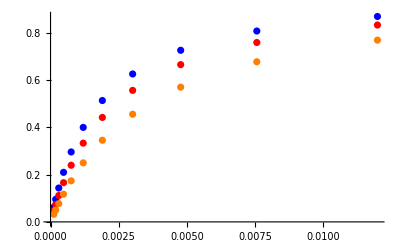

```mathematica
inhib1=inhibFittingData[[1;;11,{3,-1}]];
inhib2=inhibFittingData[[12;;22,{3,-1}]];
inhib3=inhibFittingData[[23;;33,{3,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,0.0018}

{1.,0.0024}

{1.,0.0036}

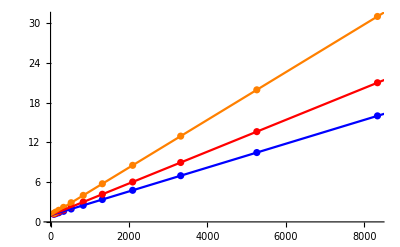

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,0,10000}, PlotStyle->{Blue,Red, Orange}]]
```

```mathematica
Dimensions@allFittingData
```

{192,11}

### Simulate data with uncertainty

```mathematica
Export["TALA2SimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions,  unifiedRateConstList, customRatiosDataList}, "MX"];

Export["TALA2SimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions,  unifiedRateConstList,  customRatiosDataList];
```

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

```mathematica
FilePrint[dataPathList[[1]]]
```

e4p[c]	f6p[c]	g3p[c]	s7p[c]	pi[c]	param_TALA2_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.7976188652987861
0	0	3.4971596682114973e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.09090909090909086
0	0	5.542624551097971e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.13680688860320997
0	0	8.784467919403012e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.20076000891310178
0	0	0.000013922443404854854	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.28474724895080117
0	0	0.000022065585774779593	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.3868631798468568
0	0	0.00003497159668211497	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.4999999999999998
0	0	0.00005542624551097971	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.613136820153143
0	0	0.00008784467919403013	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.7152527510491986
0	0	0.00013922443404854867	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.7992399910868981
0	0	0.00022065585774779593	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.8631931113967898
0	0	0.00034971596682114973	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.9090909090909091
0.000010205108679489661	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.09090909090909094
0.000016174007274448992	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.1368068886032101
0.000025634074024090747	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.20076000891310192
0.000040627269415825704	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.2847472489508017
0.00006438988272542566	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.386863179846857
0.0001020510867948966	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.5
0.00016174007274448994	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.6131368201531432
0.0002563407402409075	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.7152527510491988
0.00040627269415825665	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.7992399910868984
0.0006438988272542565	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.86319311139679
0.001020510867948966	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.9090909090909092
0.01	0.00012062499333542214	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.0909090909090909
0.01	0.00019117773077797782	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.13680688860321003
0.01	0.00030299628406018036	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.2007600089131017
0.01	0.0004802167479479938	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.28474724895080145
0.01	0.0007610922547285893	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.38686317984685686
0.01	0.0012062499333542213	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.4999999999999999
0.01	0.0019117773077797781	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.6131368201531431
0.01	0.0030299628406018067	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.7152527510491987
0.01	0.004802167479479938	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.7992399910868982
0.01	0.007610922547285893	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.8631931113967899
0.01	0.012062499333542214	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.9090909090909091
0	0	0.01	0.000028550945785075704	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.0909090909090909
0	0	0.01	0.00004525019961309282	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.13680688860321005
0	0	0.01	0.00007171673332429735	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.20076000891310186
0	0	0.01	0.00011366336243122789	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.28474724895080145
0	0	0.01	0.00018014428934949323	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.3868631798468568
0	0	0.01	0.000285509457850757	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.4999999999999999
0	0	0.01	0.00045250199613092824	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.6131368201531431
0	0	0.01	0.0007171673332429736	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.7152527510491988
0	0	0.01	0.001136633624312279	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.7992399910868984
0	0	0.01	0.0018014428934949324	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.8631931113967899
0	0	0.01	0.0028550945785075703	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.9090909090909092
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	74.73681542932354
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.03887695340406
0.01	0.00011999999999999995	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.06249999999999998
0.01	0.00037947331922020535	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.1741123948954683
0.01	0.0011999999999999995	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.3999999999999999
0.01	0.003794733192202054	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.6782688399674104
0.01	0.011999999999999995	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8695652173913043
0.01	0.00011999999999999995	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.0476190476190476
0.01	0.00037947331922020535	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.13652705949581428
0.01	0.0011999999999999995	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.33333333333333326
0.01	0.003794733192202054	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.6125741132772069
0.01	0.011999999999999995	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8333333333333333
0.01	0.00011999999999999995	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.03225806451612902
0.01	0.00037947331922020535	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.09535767393825996
0.01	0.0011999999999999995	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.2499999999999999
0.01	0.003794733192202054	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.513167019494862
0.01	0.011999999999999995	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.769230769230769
9.000000000000007e-6	0.01	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.06250000000000004
0.000028460498941515435	0.01	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.17411239489546843
0.00009000000000000007	0.01	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.40000000000000013
0.00028460498941515434	0.01	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.6782688399674106
0.0009000000000000007	0.01	0	0	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8695652173913043
9.000000000000007e-6	0.01	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.04761904761904766
0.000028460498941515435	0.01	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.1365270594958144
0.00009000000000000007	0.01	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.33333333333333354
0.00028460498941515434	0.01	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.612574113277207
0.0009000000000000007	0.01	0	0	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8333333333333336
9.000000000000007e-6	0.01	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.03225806451612906
0.000028460498941515435	0.01	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.09535767393826003
0.00009000000000000007	0.01	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.25000000000000017
0.00028460498941515434	0.01	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.5131670194948621
0.0009000000000000007	0.01	0	0	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.7692307692307694
0	0	0.01	0.0000285	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.06250000000000001
0	0	0.01	0.00009012491331479881	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.17411239489546834
0	0	0.01	0.000285	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.39999999999999997
0	0	0.01	0.0009012491331479881	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6782688399674105
0	0	0.01	0.00285	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8695652173913043
0	0	0.01	0.0000285	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.04761904761904762
0	0	0.01	0.00009012491331479881	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.13652705949581434
0	0	0.01	0.000285	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.3333333333333333
0	0	0.01	0.0009012491331479881	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6125741132772069
0	0	0.01	0.00285	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8333333333333333
0	0	0.01	0.0000285	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.03225806451612904
0	0	0.01	0.00009012491331479881	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.09535767393825997
0	0	0.01	0.000285	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.25
0	0	0.01	0.0009012491331479881	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.513167019494862
0	0	0.01	0.00285	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.7692307692307693
0	0	3.7999999999999996e-6	0.01	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.062499999999999986
0	0	0.000012016655108639841	0.01	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.17411239489546834
0	0	0.000037999999999999995	0.01	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.3999999999999999
0	0	0.0001201665510863984	0.01	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6782688399674105
0	0	0.00037999999999999997	0.01	0.008954707009168561	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8695652173913043
0	0	3.7999999999999996e-6	0.01	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.04761904761904761
0	0	0.000012016655108639841	0.01	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.1365270594958143
0	0	0.000037999999999999995	0.01	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.33333333333333326
0	0	0.0001201665510863984	0.01	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6125741132772068
0	0	0.00037999999999999997	0.01	0.017909414018337122	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8333333333333334
0	0	3.7999999999999996e-6	0.01	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.032258064516129024
0	0	0.000012016655108639841	0.01	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.09535767393825997
0	0	0.000037999999999999995	0.01	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.24999999999999997
0	0	0.0001201665510863984	0.01	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.5131670194948619
0	0	0.00037999999999999997	0.01	0.035818828036674244	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.7692307692307692
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79

### Parameter scan

```mathematica
Export["TALA2ParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						   haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList}, "MX"];

Export["TALA2ParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"inhib",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						   haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

{0.0166535,0.0166535,0.0166535,0.0166535}

Possibly there are more than one transition equation and the more than one ratio

{((TALA2^c)_^+pi^c⇌(TALA2^c&pi^c)_^)^TALA2_Kic_pi_1_f6p,((TALA2^c&mod^c)_^+pi^c⇌(TALA2^c&mod^c&pi^c)_^)^TALA2_Kic_pi_2_f6p}

{k_TALA2_Kic_pi_1_f6p^⟶,k_TALA2_Kic_pi_2_f6p^⟶}

{k_TALA2_Kic_pi_1_f6p^⟵,k_TALA2_Kic_pi_2_f6p^⟵}

```mathematica
FilePrint[dataPathList[[15]]]
```

e4p[c]	f6p[c]	g3p[c]	s7p[c]	pi[c]	param_TALA2_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt"	0.8403361344537815
0	0	3.7999999999999996e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.09090909090909091
0	0	6.022594131352233e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.13680688860321005
0	0	9.545168439736411e-6	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.20076000891310186
0	0	0.000015128072481032882	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.2847472489508012
0	0	0.00002397637909024733	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.3868631798468568
0	0	0.000037999999999999995	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.49999999999999994
0	0	0.000060225941313522335	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.6131368201531431
0	0	0.00009545168439736412	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.7152527510491987
0	0	0.00015128072481032897	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.7992399910868984
0	0	0.0002397637909024733	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.86319311139679
0	0	0.00037999999999999997	0.01	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt"	0.9090909090909091
9.000000000000007e-6	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.09090909090909098
0.000014264038732150038	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.13680688860321014
0.000022606977883586257	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.20076000891310197
0.00003582964534981475	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.2847472489508014
0.00005678616100321741	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.38686317984685703
0.00009000000000000007	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.5000000000000002
0.00014264038732150037	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.6131368201531432
0.00022606977883586258	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.7152527510491988
0.00035829645349814786	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.7992399910868985
0.0005678616100321741	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.86319311139679
0.0009000000000000007	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt"	0.9090909090909093
0.01	0.00011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.09090909090909088
0.01	0.00019018718309533363	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.13680688860321
0.01	0.0003014263717811494	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.20076000891310164
0.01	0.0004777286046641966	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.28474724895080133
0.01	0.0007571488133762321	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.38686317984685703
0.01	0.0011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.49999999999999994
0.01	0.0019018718309533362	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.613136820153143
0.01	0.0030142637178114944	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.7152527510491984
0.01	0.004777286046641966	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.7992399910868982
0.01	0.007571488133762321	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.8631931113967899
0.01	0.011999999999999995	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt"	0.9090909090909092
0	0	0.01	0.0000285	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.09090909090909093
0	0	0.01	0.000045169455985141756	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.13680688860321005
0	0	0.01	0.00007158876329802309	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.2007600089131019
0	0	0.01	0.00011346054360774674	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.28474724895080145
0	0	0.01	0.000179822843176855	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.38686317984685686
0	0	0.01	0.000285	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.5
0	0	0.01	0.00045169455985141755	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.6131368201531432
0	0	0.01	0.000715887632980231	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.7152527510491988
0	0	0.01	0.0011346054360774674	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.7992399910868982
0	0	0.01	0.00179822843176855	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.86319311139679
0	0	0.01	0.00285	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt"	0.9090909090909091
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.002	0.01	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	71.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.05	0	0	0	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	79.4
0.01	0.00011999999999999995	0	0	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.06249999999999998
0.01	0.00037947331922020535	0	0	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.1741123948954683
0.01	0.0011999999999999995	0	0	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.3999999999999999
0.01	0.003794733192202054	0	0	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.6782688399674104
0.01	0.011999999999999995	0	0	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8695652173913043
0.01	0.00011999999999999995	0	0	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.0476190476190476
0.01	0.00037947331922020535	0	0	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.13652705949581428
0.01	0.0011999999999999995	0	0	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.33333333333333326
0.01	0.003794733192202054	0	0	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.6125741132772069
0.01	0.011999999999999995	0	0	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8333333333333333
0.01	0.00011999999999999995	0	0	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.03225806451612902
0.01	0.00037947331922020535	0	0	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.09535767393825996
0.01	0.0011999999999999995	0	0	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.2499999999999999
0.01	0.003794733192202054	0	0	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.513167019494862
0.01	0.011999999999999995	0	0	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.769230769230769
9.000000000000007e-6	0.01	0	0	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.06250000000000004
0.000028460498941515435	0.01	0	0	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.17411239489546843
0.00009000000000000007	0.01	0	0	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.40000000000000013
0.00028460498941515434	0.01	0	0	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.6782688399674106
0.0009000000000000007	0.01	0	0	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8695652173913043
9.000000000000007e-6	0.01	0	0	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.04761904761904766
0.000028460498941515435	0.01	0	0	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.1365270594958144
0.00009000000000000007	0.01	0	0	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.33333333333333354
0.00028460498941515434	0.01	0	0	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.612574113277207
0.0009000000000000007	0.01	0	0	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.8333333333333336
9.000000000000007e-6	0.01	0	0	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.03225806451612906
0.000028460498941515435	0.01	0	0	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.09535767393826003
0.00009000000000000007	0.01	0	0	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.25000000000000017
0.00028460498941515434	0.01	0	0	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.5131670194948621
0.0009000000000000007	0.01	0	0	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt"	0.7692307692307694
0	0	0.01	0.0000285	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.06250000000000001
0	0	0.01	0.00009012491331479881	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.17411239489546834
0	0	0.01	0.000285	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.39999999999999997
0	0	0.01	0.0009012491331479881	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6782688399674105
0	0	0.01	0.00285	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8695652173913043
0	0	0.01	0.0000285	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.04761904761904762
0	0	0.01	0.00009012491331479881	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.13652705949581434
0	0	0.01	0.000285	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.3333333333333333
0	0	0.01	0.0009012491331479881	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6125741132772069
0	0	0.01	0.00285	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8333333333333333
0	0	0.01	0.0000285	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.03225806451612904
0	0	0.01	0.00009012491331479881	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.09535767393825997
0	0	0.01	0.000285	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.25
0	0	0.01	0.0009012491331479881	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.513167019494862
0	0	0.01	0.00285	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.7692307692307693
0	0	3.7999999999999996e-6	0.01	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.062499999999999986
0	0	0.000012016655108639841	0.01	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.17411239489546834
0	0	0.000037999999999999995	0.01	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.3999999999999999
0	0	0.0001201665510863984	0.01	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6782688399674105
0	0	0.00037999999999999997	0.01	0.00005	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8695652173913043
0	0	3.7999999999999996e-6	0.01	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.04761904761904761
0	0	0.000012016655108639841	0.01	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.1365270594958143
0	0	0.000037999999999999995	0.01	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.33333333333333326
0	0	0.0001201665510863984	0.01	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.6125741132772068
0	0	0.00037999999999999997	0.01	0.0001	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.8333333333333334
0	0	3.7999999999999996e-6	0.01	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.032258064516129024
0	0	0.000012016655108639841	0.01	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.09535767393825997
0	0	0.000037999999999999995	0.01	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.24999999999999997
0	0	0.0001201665510863984	0.01	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.5131670194948619
0	0	0.00037999999999999997	0.01	0.0002	1	8.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt"	0.7692307692307692
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79
0	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt"	125.79

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=100;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	1
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	16
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	16
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_e4p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateFor_f6p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/relRateRev_s7p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/haldaneRatio_1.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_TALA2/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFileName, lmaResultsFileName, numTrials, dataPathList]
```

best_fit: 0.971069576744
best_fit: 0.772710299882
best_fit: 13.5462298997
best_fit: 1.08552030181
best_fit: 0.962613876325
best_fit: 5.20916142412
best_fit: 5.82646324864
best_fit: 1.08884061181
best_fit: 0.945734522113
best_fit: 1.09734843498
best_fit: 2.20152462667
best_fit: 12.3962253924
best_fit: 4.06642040394
best_fit: 1.09440183702
best_fit: 9.22172151483
best_fit: 9.65169535876
best_fit: 4.97947646695
best_fit: 1.0348821169
best_fit: 18.287695211
best_fit: 5.14766246435
best_fit: 9.14252766835
best_fit: 9.2042261753
best_fit: 1.03481348814
best_fit: 1.09942138527
best_fit: 5.09358521934
best_fit: 2.22354845844
best_fit: 1.04358783844
best_fit: 7.27209902697
best_fit: 4.28090423088
best_fit: 1.09481434815
best_fit: 4.15013822017
best_fit: 4.07508482325
best_fit: 5.08526710569
best_fit: 5.01372283299
best_fit: 1.09293469995
best_fit: 4.26204069914
best_fit: 1.08884092276
best_fit: 2.20165733688
best_fit: 4.40205243541
best_fit: 1.07424274212
best_fit: 9.14878340237
best_fit: 1.01636105307
best_fit: 9.27460698068
best_fit: 1.09913509712
best_fit: 1.09995291587
best_fit: 1.02703215989
best_fit: 10.2083038837
best_fit: 5.14100853036
best_fit: 10.0922090396
best_fit: 4.06636360501
best_fit: 4.13130434192
best_fit: 5.13911015179
best_fit: 4.04629446127
best_fit: 5.19954784641
best_fit: 1.06830780091
best_fit: 9.23577101599
best_fit: 4.7043722927
best_fit: 6.24079097506
best_fit: 1.04116382106
best_fit: 1.09933017545
best_fit: 1.09249353564
best_fit: 4.28468554687
best_fit: 11.7335815897
best_fit: 1.09940515541
best_fit: 1.08659229098
best_fit: 7.26668519273
best_fit: 0.956286139431
best_fit: 4.08945732815
best_fit: 5.13553334846
best_fit: 0.970505589041
best_fit: 9.44107319168
best_fit: 4.07484129618
best_fit: 4.07823641806
best_fit: 5.07069962153
best_fit: 6.05307909054
best_fit: 0.999052317271
best_fit: 12.3999626461
best_fit: 4.08594701622
best_fit: 0.881961505095
best_fit: 6.78683073347
best_fit: 1.08273748801
best_fit: 1.09351572881
best_fit: 13.7944456322
best_fit: 1.00665720658
best_fit: 7.3352916488
best_fit: 0.955648994921
best_fit: 4.10617208158
best_fit: 1.03545378302
best_fit: 1.0681009714
best_fit: 4.11172714239
best_fit: 1.09218997618
best_fit: 7.24995290662
best_fit: 1.09270488985
best_fit: 4.09119511398
best_fit: 1.08161564121
best_fit: 18.4369763094
best_fit: 8.43369465151
best_fit: 4.18793002647
best_fit: 1.04213102197
best_fit: 1.09642272166

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(*no uncertainty or parameter scan*)
lmaResultsFileNameNew=lmaResultsFileName;
dataFilePath = dataPathList;
```

```mathematica
(*with uncertainty or parameter scan*)
datasetI=2;
lmaResultsFileNameNew=StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileName, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.0000975576 | 9.51749×10^-9 | 0.00018879 | 0.022466 | 0.840336 | 0.840525
1 | haldaneRatio_1 | 0.0000975576 | 9.51749×10^-9 | 0.00018879 | 0.022466 | 0.840336 | 0.840525
1 | haldaneRatio_1 | 0.0000975576 | 9.51749×10^-9 | 0.00018879 | 0.022466 | 0.840336 | 0.840525
1 | haldaneRatio_1 | 0.0000975576 | 9.51749×10^-9 | 0.00018879 | 0.022466 | 0.840336 | 0.840525
1 | haldaneRatio_1 | 0.0000975576 | 9.51749×10^-9 | 0.00018879 | 0.022466 | 0.840336 | 0.840525
1 | haldaneRatio_1 | 0.0000975576 | 9.51749×10^-9 | 0.00018879 | 0.022466 | 0.840336 | 0.840525
1 | haldaneRatio_1 | 0.0000975576 | 9.51749×10^-9 | 0.00018879 | 0.022466 | 0.840336 | 0.840525
1 | haldaneRatio_1 | 0.0000975576 | 9.51749×10^-9 | 0.00018879 | 0.022466 | 0.840336 | 0.840525
1 | haldaneRatio_1 | 0.0000975576 | 9.51749×10^-9 | 0.00018879 | 0.022466 | 0.840336 | 0.840525
1 | haldaneRatio_1 | 0.0000975576 | 9.51749×10^-9 | 0.00018879 | 0.022466 | 0.840336 | 0.840525
1 | haldaneRatio_1 | 0.0000975576 | 9.51749×10^-9 | 0.00018879 | 0.022466 | 0.840336 | 0.840525
1 | relRateRev_g3p | 0.0106303 | 0.000113003 | 0.00225265 | 2.47791 | 0.0909091 | 0.0931617
1 | relRateRev_g3p | 0.0100873 | 0.000101754 | 0.00321478 | 2.34987 | 0.136807 | 0.140022
1 | relRateRev_g3p | 0.00933185 | 0.0000870834 | 0.00436048 | 2.17199 | 0.20076 | 0.20512
1 | relRateRev_g3p | 0.00834174 | 0.0000695846 | 0.00552216 | 1.93932 | 0.284747 | 0.290269
1 | relRateRev_g3p | 0.00714095 | 0.0000509931 | 0.00641364 | 1.65786 | 0.386863 | 0.393277
1 | relRateRev_g3p | 0.00581443 | 0.0000338075 | 0.00673912 | 1.34782 | 0.5 | 0.506739
1 | relRateRev_g3p | 0.00449194 | 0.0000201776 | 0.00637463 | 1.03968 | 0.613137 | 0.619511
1 | relRateRev_g3p | 0.00330173 | 0.0000109015 | 0.00545845 | 0.76315 | 0.715253 | 0.720711
1 | relRateRev_g3p | 0.00232526 | 5.40685×10^-6 | 0.0042907 | 0.536848 | 0.79924 | 0.803531
1 | relRateRev_g3p | 0.00158319 | 2.50648×10^-6 | 0.00315245 | 0.365207 | 0.863193 | 0.866346
1 | relRateRev_g3p | 0.00105139 | 1.10543×10^-6 | 0.00220351 | 0.242386 | 0.909091 | 0.911294
0.1 | relRateFor_e4p | 0.0513292 | 0.00263469 | 0.0114053 | 12.5458 | 0.0909091 | 0.102314
0.1 | relRateFor_e4p | 0.048587 | 0.0023607 | 0.0161944 | 11.8374 | 0.136807 | 0.153001
0.1 | relRateFor_e4p | 0.0447948 | 0.00200657 | 0.0218127 | 10.8651 | 0.20076 | 0.222573
0.1 | relRateFor_e4p | 0.0398644 | 0.00158917 | 0.0273744 | 9.61358 | 0.284747 | 0.312122
0.1 | relRateFor_e4p | 0.0339441 | 0.0011522 | 0.03145 | 8.12948 | 0.386863 | 0.418313
0.1 | relRateFor_e4p | 0.0274778 | 0.000755029 | 0.0326572 | 6.53144 | 0.5 | 0.532657
0.1 | relRateFor_e4p | 0.0211064 | 0.000445478 | 0.0305339 | 4.97995 | 0.613137 | 0.643671
0.1 | relRateFor_e4p | 0.0154347 | 0.000238231 | 0.0258771 | 3.61789 | 0.715253 | 0.74113
0.1 | relRateFor_e4p | 0.0108249 | 0.000117178 | 0.0201716 | 2.52385 | 0.79924 | 0.819412
0.1 | relRateFor_e4p | 0.0073472 | 0.0000539813 | 0.0147273 | 1.70615 | 0.863193 | 0.87792
0.1 | relRateFor_e4p | 0.00486838 | 0.0000237012 | 0.0102481 | 1.12729 | 0.909091 | 0.919339
1 | relRateFor_f6p | 0.0721509 | 0.00520575 | 0.0164301 | 18.0731 | 0.0909091 | 0.107339
1 | relRateFor_f6p | 0.0682061 | 0.00465207 | 0.0232646 | 17.0054 | 0.136807 | 0.160072
1 | relRateFor_f6p | 0.0627685 | 0.00393989 | 0.0312174 | 15.5496 | 0.20076 | 0.231977
1 | relRateFor_f6p | 0.0557294 | 0.00310577 | 0.0389872 | 13.6919 | 0.284747 | 0.323734
1 | relRateFor_f6p | 0.0473219 | 0.00223936 | 0.044536 | 11.5121 | 0.386863 | 0.431399
1 | relRateFor_f6p | 0.0381931 | 0.00145871 | 0.0459629 | 9.19257 | 0.5 | 0.545963
1 | relRateFor_f6p | 0.0292523 | 0.000855696 | 0.042721 | 6.96761 | 0.613137 | 0.655858
1 | relRateFor_f6p | 0.0213375 | 0.000455288 | 0.0360189 | 5.03583 | 0.715253 | 0.751272
1 | relRateFor_f6p | 0.0149342 | 0.00022303 | 0.0279616 | 3.49853 | 0.79924 | 0.827202
1 | relRateFor_f6p | 0.0101208 | 0.000102432 | 0.0203522 | 2.35778 | 0.863193 | 0.883545
1 | relRateFor_f6p | 0.00669901 | 0.0000448768 | 0.0141315 | 1.55446 | 0.909091 | 0.923222
0.8 | relRateRev_s7p | 0.01155 | 0.000133404 | 0.00245016 | 2.69518 | 0.0909091 | 0.0933593
0.8 | relRateRev_s7p | 0.0109595 | 0.00012011 | 0.00349627 | 2.55563 | 0.136807 | 0.140303
0.8 | relRateRev_s7p | 0.010138 | 0.000102778 | 0.00474157 | 2.36181 | 0.20076 | 0.205502
0.8 | relRateRev_s7p | 0.00906143 | 0.0000821095 | 0.00600358 | 2.10839 | 0.284747 | 0.290751
0.8 | relRateRev_s7p | 0.00775611 | 0.0000601572 | 0.00697109 | 1.80195 | 0.386863 | 0.393834
0.8 | relRateRev_s7p | 0.00631448 | 0.0000398727 | 0.00732292 | 1.46458 | 0.5 | 0.507323
0.8 | relRateRev_s7p | 0.00487762 | 0.0000237912 | 0.00692504 | 1.12944 | 0.613137 | 0.620062
0.8 | relRateRev_s7p | 0.0035848 | 0.0000128508 | 0.00592835 | 0.828847 | 0.715253 | 0.721181
0.8 | relRateRev_s7p | 0.00252437 | 6.37244×10^-6 | 0.00465917 | 0.58295 | 0.79924 | 0.803899
0.8 | relRateRev_s7p | 0.00171863 | 2.95367×10^-6 | 0.00342267 | 0.396512 | 0.863193 | 0.866616
0.8 | relRateRev_s7p | 0.00114128 | 1.30252×10^-6 | 0.00239214 | 0.263135 | 0.909091 | 0.911483
1 | absRateFor | 6.78112×10^-6 | 4.59835×10^-11 | 0.00111484 | 0.0015614 | 71.4 | 71.3989
1 | absRateFor | 6.78112×10^-6 | 4.59835×10^-11 | 0.00111484 | 0.0015614 | 71.4 | 71.3989
1 | absRateFor | 6.78112×10^-6 | 4.59835×10^-11 | 0.00111484 | 0.0015614 | 71.4 | 71.3989
1 | absRateFor | 6.78112×10^-6 | 4.59835×10^-11 | 0.00111484 | 0.0015614 | 71.4 | 71.3989
1 | absRateFor | 6.78112×10^-6 | 4.59835×10^-11 | 0.00111484 | 0.0015614 | 71.4 | 71.3989
1 | absRateFor | 6.78112×10^-6 | 4.59835×10^-11 | 0.00111484 | 0.0015614 | 71.4 | 71.3989
1 | absRateFor | 6.78112×10^-6 | 4.59835×10^-11 | 0.00111484 | 0.0015614 | 71.4 | 71.3989
1 | absRateFor | 6.78112×10^-6 | 4.59835×10^-11 | 0.00111484 | 0.0015614 | 71.4 | 71.3989
1 | absRateFor | 6.78112×10^-6 | 4.59835×10^-11 | 0.00111484 | 0.0015614 | 71.4 | 71.3989
1 | absRateFor | 6.78112×10^-6 | 4.59835×10^-11 | 0.00111484 | 0.0015614 | 71.4 | 71.3989
1 | absRateFor | 6.78112×10^-6 | 4.59835×10^-11 | 0.00111484 | 0.0015614 | 71.4 | 71.3989
1 | absRateFor | 1.11878×10^-6 | 1.25167×10^-12 | 0.000204542 | 0.000257609 | 79.4 | 79.4002
1 | absRateFor | 1.11878×10^-6 | 1.25167×10^-12 | 0.000204542 | 0.000257609 | 79.4 | 79.4002
1 | absRateFor | 1.11878×10^-6 | 1.25167×10^-12 | 0.000204542 | 0.000257609 | 79.4 | 79.4002
1 | absRateFor | 1.11878×10^-6 | 1.25167×10^-12 | 0.000204542 | 0.000257609 | 79.4 | 79.4002
1 | absRateFor | 1.11878×10^-6 | 1.25167×10^-12 | 0.000204542 | 0.000257609 | 79.4 | 79.4002
1 | absRateFor | 1.11878×10^-6 | 1.25167×10^-12 | 0.000204542 | 0.000257609 | 79.4 | 79.4002
1 | absRateFor | 1.11878×10^-6 | 1.25167×10^-12 | 0.000204542 | 0.000257609 | 79.4 | 79.4002
1 | absRateFor | 1.11878×10^-6 | 1.25167×10^-12 | 0.000204542 | 0.000257609 | 79.4 | 79.4002
1 | absRateFor | 1.11878×10^-6 | 1.25167×10^-12 | 0.000204542 | 0.000257609 | 79.4 | 79.4002
1 | absRateFor | 1.11878×10^-6 | 1.25167×10^-12 | 0.000204542 | 0.000257609 | 79.4 | 79.4002
1 | absRateFor | 1.11878×10^-6 | 1.25167×10^-12 | 0.000204542 | 0.000257609 | 79.4 | 79.4002
0.5 | relRateFor_f6p | 0.0486324 | 0.00236511 | 0.00740567 | 11.8491 | 0.0625 | 0.0699057
0.5 | relRateFor_f6p | 0.0425487 | 0.0018104 | 0.0179217 | 10.2932 | 0.174112 | 0.192034
0.5 | relRateFor_f6p | 0.0304911 | 0.000929706 | 0.0290926 | 7.27316 | 0.4 | 0.429093
0.5 | relRateFor_f6p | 0.0160833 | 0.000258672 | 0.0255893 | 3.77274 | 0.678269 | 0.703858
0.5 | relRateFor_f6p | 0.0064488 | 0.000041587 | 0.0130084 | 1.49597 | 0.869565 | 0.882574
0.5 | relRateFor_f6p | 0.0380866 | 0.00145059 | 0.00436467 | 9.1658 | 0.047619 | 0.0519837
0.5 | relRateFor_f6p | 0.0343863 | 0.00118242 | 0.0112493 | 8.23964 | 0.136527 | 0.147776
0.5 | relRateFor_f6p | 0.0263059 | 0.000691999 | 0.0208145 | 6.24436 | 0.333333 | 0.354148
0.5 | relRateFor_f6p | 0.0150928 | 0.000227793 | 0.0216627 | 3.53634 | 0.612574 | 0.634237
0.5 | relRateFor_f6p | 0.0064286 | 0.0000413269 | 0.0124271 | 1.49125 | 0.833333 | 0.84576
0.5 | relRateFor_f6p | 0.029961 | 0.000897661 | 0.00230397 | 7.14231 | 0.0322581 | 0.034562
0.5 | relRateFor_f6p | 0.0279432 | 0.000780822 | 0.00633715 | 6.64566 | 0.0953577 | 0.101695
0.5 | relRateFor_f6p | 0.0230373 | 0.000530716 | 0.0136194 | 5.44774 | 0.25 | 0.263619
0.5 | relRateFor_f6p | 0.0148139 | 0.00021945 | 0.0178062 | 3.46986 | 0.513167 | 0.530973
0.5 | relRateFor_f6p | 0.00695913 | 0.0000484295 | 0.0124254 | 1.61531 | 0.769231 | 0.781656
0.5 | relRateFor_e4p | 0.0315971 | 0.00099838 | 0.0047167 | 7.54671 | 0.0625 | 0.0672167
0.5 | relRateFor_e4p | 0.0277126 | 0.000767989 | 0.0114724 | 6.58905 | 0.174112 | 0.185585
0.5 | relRateFor_e4p | 0.0199556 | 0.000398226 | 0.0188086 | 4.70215 | 0.4 | 0.418809
0.5 | relRateFor_e4p | 0.0105864 | 0.000112072 | 0.0167367 | 2.46757 | 0.678269 | 0.695006
0.5 | relRateFor_e4p | 0.00426085 | 0.0000181548 | 0.00857326 | 0.985925 | 0.869565 | 0.878138
0.5 | relRateFor_e4p | 0.0328731 | 0.00108064 | 0.00374435 | 7.86314 | 0.047619 | 0.0513634
0.5 | relRateFor_e4p | 0.0296968 | 0.000881898 | 0.00966221 | 7.07714 | 0.136527 | 0.146189
0.5 | relRateFor_e4p | 0.0227473 | 0.000517439 | 0.0179245 | 5.37735 | 0.333333 | 0.351258
0.5 | relRateFor_e4p | 0.0130739 | 0.000170927 | 0.0187212 | 3.05615 | 0.612574 | 0.631295
0.5 | relRateFor_e4p | 0.0055761 | 0.0000310929 | 0.0107685 | 1.29222 | 0.833333 | 0.844102
0.5 | relRateFor_e4p | 0.0536473 | 0.00287803 | 0.00424132 | 13.1481 | 0.0322581 | 0.0364994
0.5 | relRateFor_e4p | 0.04994 | 0.002494 | 0.0116206 | 12.1863 | 0.0953577 | 0.106978
0.5 | relRateFor_e4p | 0.0409858 | 0.00167984 | 0.0247425 | 9.89699 | 0.25 | 0.274742
0.5 | relRateFor_e4p | 0.0261598 | 0.000684336 | 0.0318607 | 6.20863 | 0.513167 | 0.545028
0.5 | relRateFor_e4p | 0.0122041 | 0.00014894 | 0.0219227 | 2.84996 | 0.769231 | 0.791154
0.5 | relRateRev_s7p | 0.0156484 | 0.000244872 | 0.00221189 | 3.53903 | 0.0625 | 0.0602881
0.5 | relRateRev_s7p | 0.0138147 | 0.000190846 | 0.00545127 | 3.13089 | 0.174112 | 0.168661
0.5 | relRateRev_s7p | 0.0100797 | 0.0001016 | 0.00917683 | 2.29421 | 0.4 | 0.390823
0.5 | relRateRev_s7p | 0.00543399 | 0.0000295283 | 0.00843378 | 1.24343 | 0.678269 | 0.669835
0.5 | relRateRev_s7p | 0.00221123 | 4.88952×10^-6 | 0.00441617 | 0.507859 | 0.869565 | 0.865149
0.5 | relRateRev_s7p | 0.0286694 | 0.000821935 | 0.003042 | 6.3882 | 0.047619 | 0.044577
0.5 | relRateRev_s7p | 0.0260717 | 0.000679733 | 0.00795487 | 5.82659 | 0.136527 | 0.128572
0.5 | relRateRev_s7p | 0.0202655 | 0.000410692 | 0.015197 | 4.55911 | 0.333333 | 0.318136
0.5 | relRateRev_s7p | 0.0118919 | 0.000141417 | 0.016546 | 2.70106 | 0.612574 | 0.596028
0.5 | relRateRev_s7p | 0.00515573 | 0.0000265815 | 0.00983442 | 1.18013 | 0.833333 | 0.823499
0.5 | relRateRev_s7p | 0.0405907 | 0.0016476 | 0.00287835 | 8.92287 | 0.0322581 | 0.0293797
0.5 | relRateRev_s7p | 0.0380566 | 0.0014483 | 0.0080004 | 8.38989 | 0.0953577 | 0.0873573
0.5 | relRateRev_s7p | 0.0317829 | 0.00101015 | 0.0176423 | 7.0569 | 0.25 | 0.232358
0.5 | relRateRev_s7p | 0.0208935 | 0.000436539 | 0.0241036 | 4.69702 | 0.513167 | 0.489063
0.5 | relRateRev_s7p | 0.0100294 | 0.000100588 | 0.0175607 | 2.28289 | 0.769231 | 0.75167
0.5 | relRateRev_g3p | 0.0260833 | 0.000680337 | 0.00364319 | 5.8291 | 0.0625 | 0.0588568
0.5 | relRateRev_g3p | 0.0230589 | 0.000531712 | 0.00900337 | 5.17101 | 0.174112 | 0.165109
0.5 | relRateRev_g3p | 0.0168727 | 0.000284689 | 0.0152424 | 3.81059 | 0.4 | 0.384758
0.5 | relRateRev_g3p | 0.0091289 | 0.0000833368 | 0.0141085 | 2.08007 | 0.678269 | 0.66416
0.5 | relRateRev_g3p | 0.00372416 | 0.0000138693 | 0.0074248 | 0.853852 | 0.869565 | 0.86214
0.5 | relRateRev_g3p | 0.0404007 | 0.00163222 | 0.00423001 | 8.88303 | 0.047619 | 0.043389
0.5 | relRateRev_g3p | 0.0367843 | 0.00135308 | 0.0110875 | 8.12111 | 0.136527 | 0.12544
0.5 | relRateRev_g3p | 0.0286702 | 0.000821978 | 0.0212945 | 6.38836 | 0.333333 | 0.312039
0.5 | relRateRev_g3p | 0.0168908 | 0.0002853 | 0.0233672 | 3.8146 | 0.612574 | 0.589207
0.5 | relRateRev_g3p | 0.00734692 | 0.0000539773 | 0.0139789 | 1.67746 | 0.833333 | 0.819354
0.5 | relRateRev_g3p | 0.047711 | 0.00227634 | 0.0033561 | 10.4039 | 0.0322581 | 0.028902
0.5 | relRateRev_g3p | 0.0447548 | 0.002003 | 0.0093374 | 9.79198 | 0.0953577 | 0.0860203
0.5 | relRateRev_g3p | 0.0374238 | 0.00140054 | 0.0206408 | 8.25631 | 0.25 | 0.229359
0.5 | relRateRev_g3p | 0.0246562 | 0.000607928 | 0.0283225 | 5.51915 | 0.513167 | 0.484845
0.5 | relRateRev_g3p | 0.0118622 | 0.000140712 | 0.0207262 | 2.69441 | 0.769231 | 0.748505
0.5 | inhibRatio_pi_1 | 0.085725 | 0.00734878 | 0.00340345 | 17.9129 | 0.019 | 0.0155966
0.5 | inhibRatio_pi_1 | 0.085725 | 0.00734878 | 0.00340345 | 17.9129 | 0.019 | 0.0155966
0.5 | inhibRatio_pi_1 | 0.085725 | 0.00734878 | 0.00340345 | 17.9129 | 0.019 | 0.0155966
0.5 | inhibRatio_pi_1 | 0.085725 | 0.00734878 | 0.00340345 | 17.9129 | 0.019 | 0.0155966
0.5 | inhibRatio_pi_1 | 0.085725 | 0.00734878 | 0.00340345 | 17.9129 | 0.019 | 0.0155966
0.5 | inhibRatio_pi_1 | 0.085725 | 0.00734878 | 0.00340345 | 17.9129 | 0.019 | 0.0155966
0.5 | inhibRatio_pi_1 | 0.085725 | 0.00734878 | 0.00340345 | 17.9129 | 0.019 | 0.0155966
0.5 | inhibRatio_pi_1 | 0.085725 | 0.00734878 | 0.00340345 | 17.9129 | 0.019 | 0.0155966
0.5 | inhibRatio_pi_1 | 0.085725 | 0.00734878 | 0.00340345 | 17.9129 | 0.019 | 0.0155966
0.5 | inhibRatio_pi_1 | 0.085725 | 0.00734878 | 0.00340345 | 17.9129 | 0.019 | 0.0155966
0.5 | inhibRatio_pi_1 | 0.085725 | 0.00734878 | 0.00340345 | 17.9129 | 0.019 | 0.0155966
0.5 | inhibRatio_pi_2 | 0.126962 | 0.0161194 | 0.00481623 | 25.3486 | 0.019 | 0.0141838
0.5 | inhibRatio_pi_2 | 0.126962 | 0.0161194 | 0.00481623 | 25.3486 | 0.019 | 0.0141838
0.5 | inhibRatio_pi_2 | 0.126962 | 0.0161194 | 0.00481623 | 25.3486 | 0.019 | 0.0141838
0.5 | inhibRatio_pi_2 | 0.126962 | 0.0161194 | 0.00481623 | 25.3486 | 0.019 | 0.0141838
0.5 | inhibRatio_pi_2 | 0.126962 | 0.0161194 | 0.00481623 | 25.3486 | 0.019 | 0.0141838
0.5 | inhibRatio_pi_2 | 0.126962 | 0.0161194 | 0.00481623 | 25.3486 | 0.019 | 0.0141838
0.5 | inhibRatio_pi_2 | 0.126962 | 0.0161194 | 0.00481623 | 25.3486 | 0.019 | 0.0141838
0.5 | inhibRatio_pi_2 | 0.126962 | 0.0161194 | 0.00481623 | 25.3486 | 0.019 | 0.0141838
0.5 | inhibRatio_pi_2 | 0.126962 | 0.0161194 | 0.00481623 | 25.3486 | 0.019 | 0.0141838
0.5 | inhibRatio_pi_2 | 0.126962 | 0.0161194 | 0.00481623 | 25.3486 | 0.019 | 0.0141838
0.5 | inhibRatio_pi_2 | 0.126962 | 0.0161194 | 0.00481623 | 25.3486 | 0.019 | 0.0141838
1 | customRatio_1 | 0.0000231906 | 5.37805×10^-10 | 0.0067168 | 0.0053397 | 125.79 | 125.783
1 | customRatio_1 | 0.0000231906 | 5.37805×10^-10 | 0.0067168 | 0.0053397 | 125.79 | 125.783
1 | customRatio_1 | 0.0000231906 | 5.37805×10^-10 | 0.0067168 | 0.0053397 | 125.79 | 125.783
1 | customRatio_1 | 0.0000231906 | 5.37805×10^-10 | 0.0067168 | 0.0053397 | 125.79 | 125.783
1 | customRatio_1 | 0.0000231906 | 5.37805×10^-10 | 0.0067168 | 0.0053397 | 125.79 | 125.783
1 | customRatio_1 | 0.0000231906 | 5.37805×10^-10 | 0.0067168 | 0.0053397 | 125.79 | 125.783
1 | customRatio_1 | 0.0000231906 | 5.37805×10^-10 | 0.0067168 | 0.0053397 | 125.79 | 125.783
1 | customRatio_1 | 0.0000231906 | 5.37805×10^-10 | 0.0067168 | 0.0053397 | 125.79 | 125.783
1 | customRatio_1 | 0.0000231906 | 5.37805×10^-10 | 0.0067168 | 0.0053397 | 125.79 | 125.783
1 | customRatio_1 | 0.0000231906 | 5.37805×10^-10 | 0.0067168 | 0.0053397 | 125.79 | 125.783
1 | customRatio_1 | 0.0000231906 | 5.37805×10^-10 | 0.0067168 | 0.0053397 | 125.79 | 125.783

### Simulated Data and Best Fit Data Plot

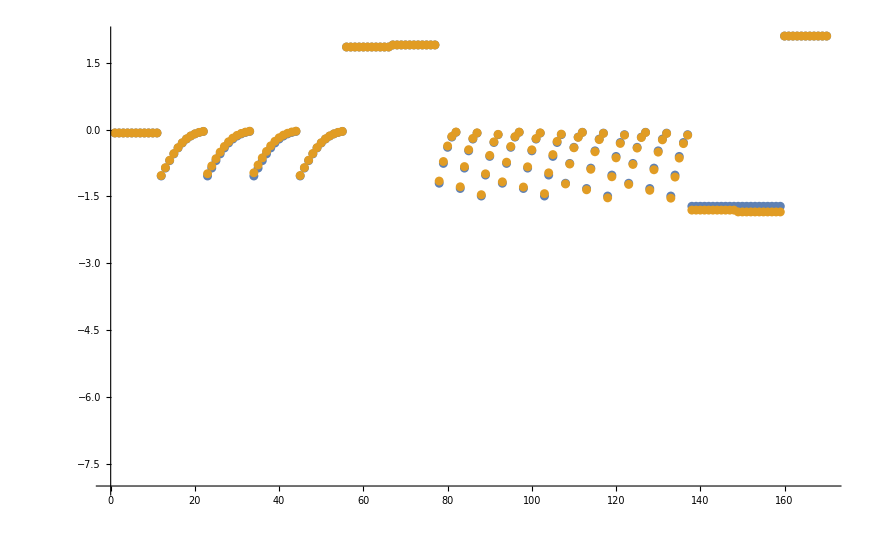

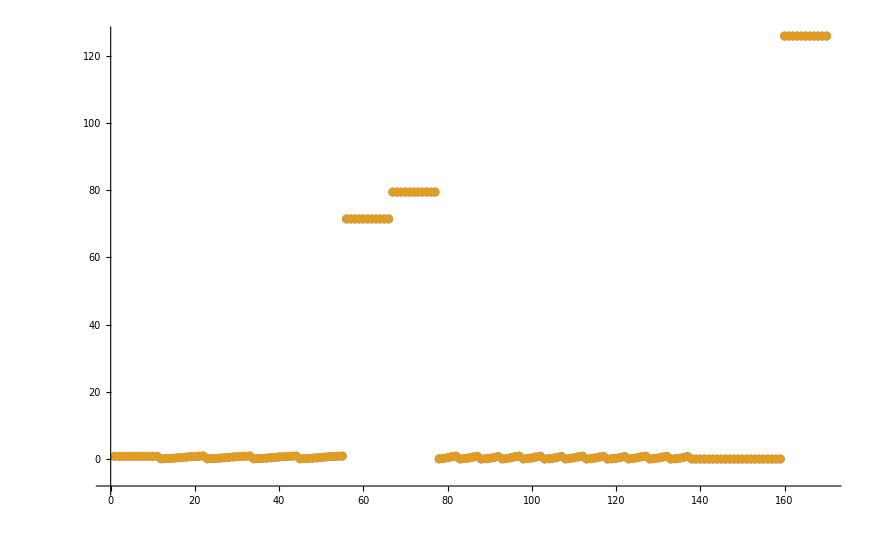

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

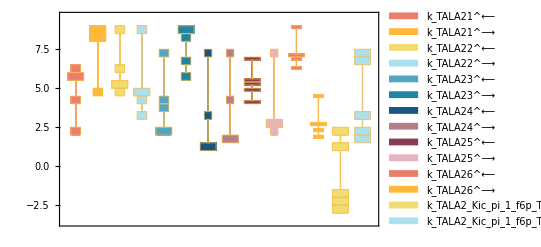

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

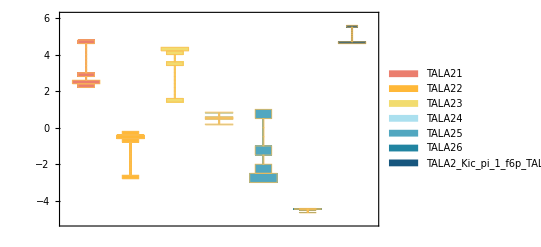

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

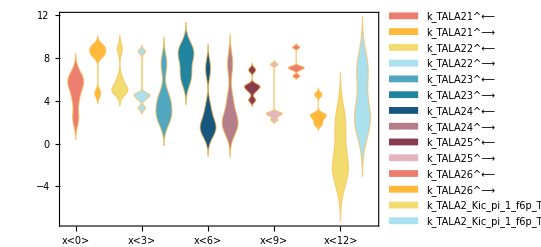

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

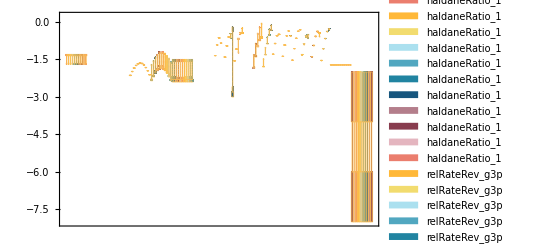

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList[[{1,2,4,5}]], absoluteRateForward/.m["pi","c"]-> 0, absoluteRateReverse/.m["pi","c"]-> 0, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.000038 | 0.000035798 | 5.79467
0.00009 | 0.0000219601 | 75.5999
0.0012 | 0.00131506 | 9.58806
0.000285 | 0.000301835 | 5.90696

```mathematica
backCalculateKcats[rxn, kcatList,absoluteRateForward/.m["pi","c"]-> 0, absoluteRateReverse/.m["pi","c"]-> 0, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
71.4 | 71.3955 | 0.00633007
79.4 | 71.3955 | 10.0813

```mathematica
backCalculateRatios[customRatiosList[[1]][[1]], customRatiosList[[1]][[2]], paramFitSub]//TableForm
```

data value | predicted value | error in %
125.79 | 125.79 | 2.31817×10^-7

```mathematica
backCalculateRatios[haldaneRatiosList[[1]][[1]], haldaneRatiosList[[1]][[2]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.840336 | 0.791753 | 5.78138